Load doze packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

Conductivity Ratio in Linear Regime

```mathematica
ratio=Gamma[κ]/(√(κ-3/2)Gamma[κ-1/2]);
```

```mathematica
ratio/.κ->2.45
```

1.34462

Ratio of J-V Relations

```mathematica
FullSimplify[JVKappa[pot,RB,Tm,nm,kappa]/JVMaxwellian[pot,RB,Tm,nm]]
```

(1. (1-((-1+RB) (1+pot/((-3/2+kappa) (-1+RB) Tm))^(1-kappa))/RB) √(Tm-(3 Tm)/(2 kappa)) Gamma[1+kappa])/((-1+kappa) √kappa (1+ⅇ^(pot/(Tm-RB Tm)) (-1+1/RB)) √Tm Gamma[-1/2+kappa])

```mathematica
JVRatio[pot_,RB_,Tm_,kappa_]:=√(1-3/(2 kappa))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])1/(1-1/kappa)(1-(1-1/RB) (1+pot/((kappa-3/2) (RB-1) Tm))^(1-kappa))/(1-(1-1/RB)ⅇ^(-pot/(Tm(RB-1))))
```

```mathematica
Manipulate[LogLinearPlot[JVRatio[pot,RB,Tm,kappa],{pot,10,100000}],{{RB,10},2,10000},{{Tm,100},20,1000},{{kappa,2.45},1.501,10}]
```

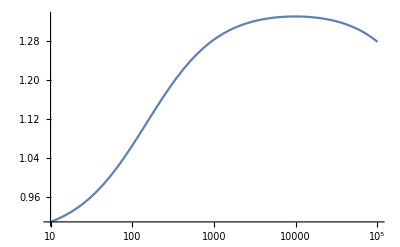

```mathematica
LogLinearPlot[JVRatio[pot,10000,150,2.45],{pot,10,100000}]
```

What’s the max, anyway? Apparently for κ = 2.45, R_B→ ∞, it gets no better than 1.33.
For κ=2.45, R_B = 4.7, it is no better than 1.

```mathematica
FindMaximum[JVRatio[pot,10000,150,3],pot]
```

{1.21987,{pot→10526.8}}

```mathematica
FindMaximum[JVRatio[pot,4.699,150,2.45],pot]
```

{1.,{pot→125.012}}

```mathematica
FindMaximum[JVRatio[pot,10000,15,2.45],pot]
```

{1.33084,{pot→984.565}}

```mathematica
JEVKappa[pot,RB,Tm,nm,kappa]/JEVMaxwellian[pot,RB,Tm,nm]
```

(1. (1-3/(2 kappa))^(3/2) √kappa (2-(1+kappa/((-1+kappa) (-1+RB))) (1-1/RB) ((-2+kappa)/(-1+kappa)+((-2+kappa) pot)/((-3/2+kappa) Tm)) (1+pot/((-3/2+kappa) (-1+RB) Tm))^(1-kappa)-(1+(1+kappa/(-1+RB))/(-1+kappa)) (1-1/RB)^2 (1+pot/((-3/2+kappa) (-1+RB) Tm))^(2-kappa)+((-2+kappa) pot)/((-3/2+kappa) Tm)) Gamma[1+kappa])/((-2+kappa) (-1+kappa) (2-ⅇ^(-pot/((-1+RB) Tm)) (2 (1-1/RB)+pot/Tm)+pot/Tm) Gamma[-1/2+kappa])

```mathematica
JEVKappa[pot,RB,Tm,nm,kappa]
```

(0.0000268059 (1-3/(2 kappa))^(3/2) √kappa nm RB (2-(1+kappa/((-1+kappa) (-1+RB))) (1-1/RB) ((-2+kappa)/(-1+kappa)+((-2+kappa) pot)/((-3/2+kappa) Tm)) (1+pot/((-3/2+kappa) (-1+RB) Tm))^(1-kappa)-(1+(1+kappa/(-1+RB))/(-1+kappa)) (1-1/RB)^2 (1+pot/((-3/2+kappa) (-1+RB) Tm))^(2-kappa)+((-2+kappa) pot)/((-3/2+kappa) Tm)) Tm^(3/2) Gamma[1+kappa])/((-2+kappa) (-1+kappa) Gamma[-1/2+kappa])

```mathematica
JEVMaxwellian[pot,RB,Tm,nm]
```

0.0000268059 nm RB (2-ⅇ^(-pot/((-1+RB) Tm)) (2 (1-1/RB)+pot/Tm)+pot/Tm) Tm^(3/2)

Ratio of J_E-V Relations

```mathematica
FullSimplify[JEVKappa[pot,RB,Tm,nm,kappa]/JEVMaxwellian[pot,RB,Tm,nm]]
```

(0.353553 (-3+2 kappa)^(3/2) (2-((-2+kappa) (1+kappa/((-1+kappa) (-1+RB))) (-1+RB) (1/(-1+kappa)+pot/((-3/2+kappa) Tm)) (1+pot/((-3/2+kappa) (-1+RB) Tm))^(1-kappa))/RB-(kappa (-1+RB) (1+pot/((-3/2+kappa) (-1+RB) Tm))^(2-kappa))/((-1+kappa) RB)+((-2+kappa) pot)/((-3/2+kappa) Tm)) Gamma[1+kappa])/((-2+kappa) (-1+kappa) kappa (2+ⅇ^(pot/(Tm-RB Tm)) (-2+2/RB-pot/Tm)+pot/Tm) Gamma[-1/2+kappa])

```mathematica
JEVRatio[pot_,RB_,Tm_,kappa_]:=(0.35355339059327373 (-3+2 kappa)^(3/2) (2-((-2+kappa) (1+kappa/((-1+kappa) (-1+RB))) (-1+RB) (1/(-1+kappa)+pot/((-3/2+kappa) Tm)) (1+pot/((-3/2+kappa) (-1+RB) Tm))^(1-kappa))/RB-(kappa (-1+RB) (1+pot/((-3/2+kappa) (-1+RB) Tm))^(2-kappa))/((-1+kappa) RB)+((-2+kappa) pot)/((-3/2+kappa) Tm)) Gamma[1+kappa])/((-2+kappa) (-1+kappa) kappa (2+ⅇ^(pot/(Tm-RB Tm)) (-2+2/RB-pot/Tm)+pot/Tm) Gamma[-1/2+kappa])
```

```mathematica
FindMaximum[{JEVRatio[pot,10000,temp,2.45],temp*5/4<pot<10000},pot]/.temp->6000
```

{1.16251,{pot→7500.03}}

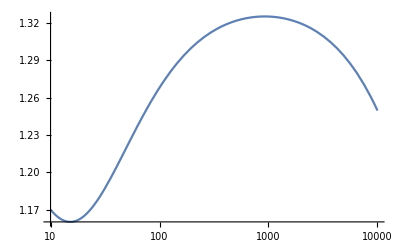

```mathematica
LogLinearPlot[JEVRatio[pot,10000,10,2.45],{pot,10,10000}]
```

```mathematica
Manipulate[ContourPlot[JEVRatio[10^logpot,10^logRB,10^logtemp,2.45],{logpot,1,5},{logRB,1,7},PlotLegends->Automatic,Frame->True,FrameLabel->{"logpot","logRB"}],{logtemp,1,3}]
```